# VISUALIZACIÓN Y EXPLORACIÓN

## Listas, tablas y gráficas

una lista es {a,b,c}. Table[expresion, {tabla}] repite expresion variando x. Plot[f,{tabla}]. Graficar funciones; ListPlot[tabla, PlotStyle->{Red, PointSize[0.02]}] grafica puntos, Manipulate agrega controles para ver como cambia el resultado al varia parámetros.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]:=2*x-3
```

```mathematica
tabla=Table[{x,f[x]},{x,0,5}]
```

{{0,-3},{1,-1},{2,1},{3,3},{4,5},{5,7}}

```mathematica
?Prepend
```

```mathematica
Grid[Prepend[tabla,{"x","f(x)"}], Frame->All]
```

x | f(x)
0 | -3
1 | -1
2 | 1
3 | 3
4 | 5
5 | 7

```mathematica
?Grid
```

Sirve para hacer las clásicas formas de correspondencia entre abscisa y ordenada.

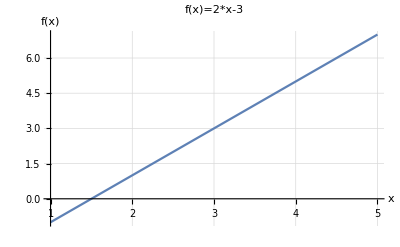

```mathematica
Plot[f[x],{x,1,5},AxesLabel->{"x","f(x)"}, PlotLabel->"f(x)=2*x-3",GridLines->Automatic]
```

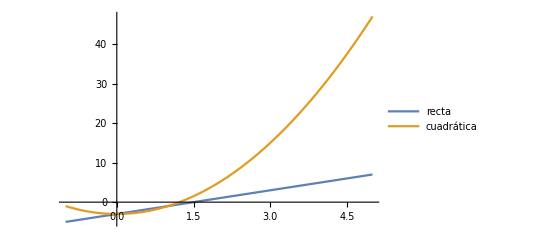

```mathematica
Plot[{f[x],2 x*x-3},{x,-1,5},PlotLegends->{"recta","cuadrática"}]
```

Podemos ver que Plot[,] suele sus opciones manejar { } en listas

```mathematica
Solve[f[x]==2x*x-3,x]
```

{{x→0},{x→1}}

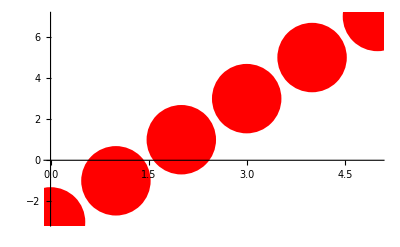

```mathematica
ListPlot[tabla,PlotStyle->{Red,PointSize[0.2]}]
```

```mathematica
Plot3D[Sin[x]*Cos[y],{x,0,2*Pi},{y,0,2 Pi}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[a*x*x+b*x+c,{x,-5,5},PlotRange->{-16,16}], {{a,1},-3,3},{{b,5},-5,5},{{c,0},-5,5}]
```

Manipulate[] lleva dentro plot[], luego otra opcion siempre lleva PlotRange{} donde { } en vez de []

```mathematica
Table[Exp[x],{x,0,5}]
```

{1,ⅇ,ⅇ^2,ⅇ^3,ⅇ^4,ⅇ^5}

## Animación con sliders: Un vértice que dibuja su trayectoria.

Un lugar geométrico es el conjunto de posiciones que toma un punto cuando cambia un parámetro s. Si calculas muchos puntos seguidos con Table y los unes con Line, obtienes una línea continua; con pocos puntos se nota la poligonal. Manipulate pone el slider; Animate lo mueve solo; Export guarda un Gif.

```mathematica
ClearAll["Global'*"]
```

```mathematica
Manipulate[Plot[Sin[x],{x,0,a},PlotRange->{{0,2 Pi},{-1.2,1.2}},PlotStyle->{Red,Thick},AxesLabel->{"x","sin x"}], {{a,1},0.05,2 Pi, Appearance -> "Labeled"}]
```

```mathematica
?Appearance
```

Aquí lo que hace que cambie es Appearance.

```mathematica
cuadro[t_] := Graphics[{
{LightGray, Line[{{-40, 0}, {14, 0}}]},
{Blue, Circle[{t, 1}, 1]},
{Red, Thick, Line[Table[{u - Sin[u], 1 - Cos[u]}, {u, 0, t, t/60}]]},
{Gray, Line[{{t, 1}, {t - Sin[t], 1 - Cos[t]}}]},
{Red, PointSize[0.025], Point[{t - Sin[t], 1 - Cos[t]}]}},
PlotRange -> {{-1, 14}, {-0.5, 2.5}}, Axes -> True, ImageSize -> 900]
Manipulate[cuadro[t], {{t, 0.1}, 0.1, 4 Pi, Appearance -> "Labeled"}]
```

```mathematica
cuadro[t_] := Graphics[{
{LightGray, Line[{{-14, 0}, {14, 0}}]},
{Blue, Circle[{t, 1}, 1]},
{Red, Thick, Line[Table[{u - Sin[u], 1 - Cos[u]}, {u, 0, t, t/60}]]},
{Gray, Line[{{t, 1}, {t - Sin[t], 1 - Cos[t]}}]},
{Red, PointSize[0.025], Point[{t - Sin[t], 1 - Cos[t]}]}},
PlotRange -> {{-1, 14}, {-0.5, 2.5}}, Axes -> True, ImageSize -> 600]
Manipulate[cuadro[t], {{t, 0.1}, 0.1, 4 Pi, Appearance -> "Labeled"}]
Carpeta=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"evidencias"}]; 
If[!DirectoryQ[carpetaaguardar],CreateDirectory[Carpeta]];
Export[FileNameJoin[{carpetaaguardar,"cicloide.gif"}],Table[cuadro[t],{t,0.1,4 Pi, 0.4}]]
```

NotebookDirectory::nosv: The notebook 87n6h_shm is not saved.

ParentDirectory::nums: Argument $Failed should be a positive machine-size integer, a nonempty string, or a File specification.

DirectoryQ::badfile: The specified argument carpetaaguardar should be a valid string or File.

Export::chtype: First argument FileNameJoin[{carpetaaguardar,cicloide.gif}] is not a valid file specification.

$Failed

```mathematica
punto[tipo_,s_]:=Switch[tipo,"recta",{s,0.5 s+1},"circulo",{3 Cos[s],3 Sin[s]},"parabola",{s-3,(s-3)^2/3}]
Manipulate[Graphics[{{Blue,Thick,Line[Table[punto[tipo,u],{u,0.01,s,s/80}]]},{Orange,EdgeForm[Black],Polygon[{{-1,0},{1,0},punto[tipo,s]}]},{Red,PointSize[0.03],Point[punto[tipo,s]]}},PlotRange->{{-5,8},{-4,6}},Axes->True,ImageSize->500],{{s,1},0.1,6,Appearance->"Labeled"},{{tipo,"recta"},{"recta","circulo","parabola"}}]
```

```mathematica
Animate[Plot[Sin[x-t],{x,0,4 Pi},PlotRange->{-1.2,1.2}],{t,0,2 Pi},AnimationRunning->False]
```

```mathematica
Animate[Plot[Sin[z-t],{z,0,4  Pi},PlotRange->{-1.2,1.2}],{t,0,2 Pi},AnimationRunning->True]
```

```mathematica
Animate[Graphics[{
{LightGray, Line[{{-14, 0}, {14, 0}}]},
{Blue, Circle[{t, 1}, 1]},
{Red, Thick, Line[Table[{u - Sin[u], 1 - Cos[u]}, {u, 0, t, t/60}]]},
{Gray, Line[{{t, 1}, {t - Sin[t], 1 - Cos[t]}}]},
{Red, PointSize[0.025], Point[{t - Sin[t], 1 - Cos[t]}]}},
PlotRange -> {{-1, 14}, {-0.5, 2.5}},Axes -> True, ImageSize -> 600],{t,0.4,4*Pi},AnimationRunning->True]
```